```mathematica
a=Import["~/fw-517-2025-02-26/ACS_LOG_2025-02-22_H16_M46_S14.csv","CSV"];
```

```mathematica
a[[Length[a]]]
```

{2025 Feb 25 15:14:06.109,253672.,200703.,19.4375,0.,0.,17.875,17.375,-11.9375,18.125,17.625,20.6875,18.6875,0}

```mathematica
Length[a[[1]]]
```

14

```mathematica
a[[Length[a]]]
```

{2025 Feb 25 15:14:06.109,253672.,200703.,19.4375,0.,0.,17.875,17.375,-11.9375,18.125,17.625,20.6875,18.6875,0}

```mathematica
b=Transpose[a];
```

```mathematica
c1=Table[{b[[2,i]],b[[9,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g1=ListPlot[c1,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

-Graphics-

```mathematica
c2=Table[{b[[2,i]],b[[10,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g2=ListPlot[c2,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

-Graphics-

```mathematica
c5=Table[{b[[2,i]],b[[12,i]]},{i,Length[b[[2]]]}];
```

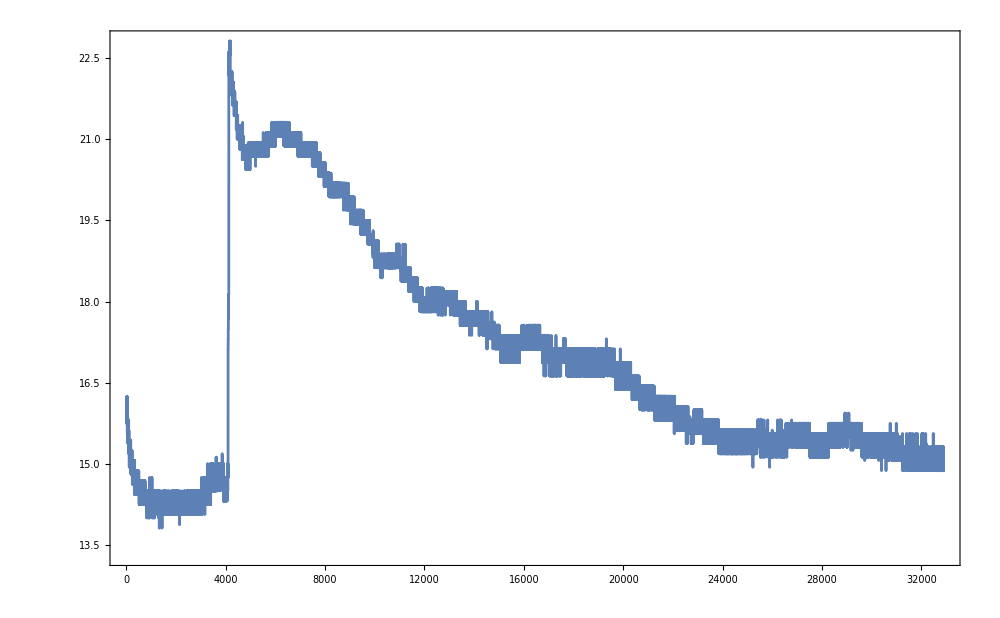

```mathematica
g5=ListPlot[c5,ImageSize->1000,PlotRange->All,Axes->False,Frame->True,Joined->True]
```

```mathematica
c4=Table[{b[[2,i]],b[[13,i]]},{i,Length[b[[2]]]}];
```

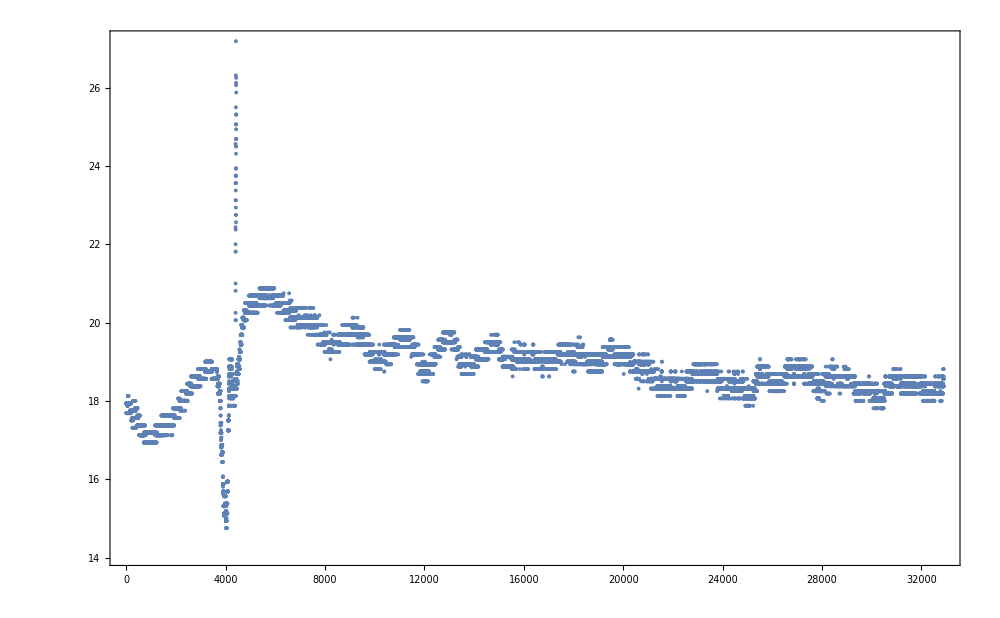

```mathematica
g4=ListPlot[c4,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
c3=Table[{b[[2,i]],b[[13,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g3=ListPlot[c4,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

-Graphics-